## Solving Kepler’s Mean Anomaly Equation Using Lagrange Series

```mathematica
Clear["Global`*"]
```

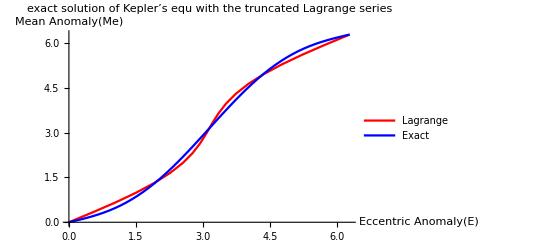

```mathematica
ecc= 0.65;(*Values from example 3.8 Chapter 3*)
(*Me = 3.6029;(*Values from example 3.8 Chapter 3*)*)
p=20;
Ea =Array[0&,p];
Me=Array[#&,p,{0,2Pi}];
(*Lagrange*)
nFinal=20;
For[i =1,i≤p,i++,
sumA = 0;
For[n=1,n≤nFinal,n++,
sumk=0;
For [k=0,k≤Floor[n/2],k++,sumK=sumk+(-1)^k 1/((n-k)!k!)(n-2k)^(n-1)Sin[(n-2k)Me[[i]]];];
a=1/2^(n-1)sumK;
sumA =sumA + a ecc^n;];
Ea[[i]] =Me[[i]]+sumA;];
h1=ListLinePlot[Transpose[{Ea,Me}],PlotStyle->Red,PlotLegends->Placed[{"Lagrange"},Right]];
h2=Plot[Ea2-ecc Sin[Ea2],{Ea2,0,2Pi},PlotStyle->Blue,PlotLegends->Placed[{"Exact"},Right]];
Show [h1,h2,
PlotLabel->"exact solution of Kepler’s equ with the truncated Lagrange series",
AxesLabel->{"Eccentric Anomaly(E)","Mean Anomaly(Me)"}]
```